```mathematica
计算两个线圈产生的电力线——折线法
```

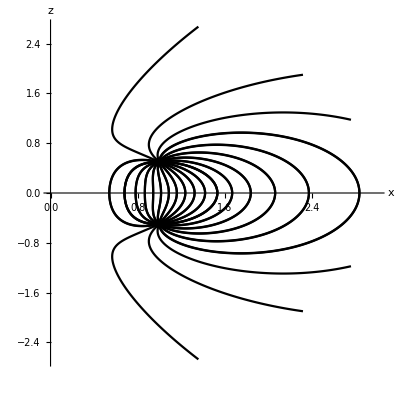

```mathematica
V0[z_,ρ_,R_]:=(2EllipticK[-(2R*ρ)/(z^2+(R-ρ)^2)])/(√(z^2+(R-ρ)^2))+
(2EllipticK[(2R*ρ)/(z^2+(R+ρ)^2)])/(√(z^2+(R+ρ)^2));d=1.0;R=1.0;
V1[z_,ρ_,R_]:=V0[z-d/2,ρ,R];
V2[z_,ρ_,R_]:=-V0[z+d/2,ρ,R];
V[z_,ρ_,R_]:=V1[z,ρ,R]+V2[z,ρ,R];
field=-D[V[z,ρ,R],ρ]-ⅈ*D[V[z,ρ,R],z];
p1={R,d/2};p2={R,-d/2};r1=0.003;r2=3.0;
step=0.005;forceline={};
Do[
θ=ϕ;single={p1};
Label[ss];p=Last[single];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];
If[(Norm[p1-p]>r1)∧(Norm[p2-p]>r1)∧
(Norm[p]<r2),AppendTo[single,p];Goto[ss]];
AppendTo[forceline,single],
{ϕ,-π,π,π/10}]
g1=Show[
Graphics[{Thickness[0.004],Line/@forceline}]];
forceline={};
Do[
θ=ϕ;single={p2};
Label[ss];p=Last[single];
p=p-step*{Cos[θ],Sin[θ]};
θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];
If[(Norm[p1-p]>r1)∧(Norm[p2-p]>r1)∧
(Norm[p]<r2),AppendTo[single,p];Goto[ss]];
AppendTo[forceline,single],
{ϕ,-π,π,π/10}]
g2=Show[
Graphics[{Thickness[0.004],Line/@forceline}]];
Show[{g1,g2},AxesStyle->Thickness[0.003],
AxesLabel->{"x","z"},AspectRatio->1,
PlotRange->{{0,r2},All},Axes->True,
AxesOrigin->{0,0}]
Clear[V,V0,V1,V2,d]
```